```mathematica
Lx=60;
Ly=60;
A=Lx*Ly;
```

```mathematica
m0 = 1;
```

```mathematica
LineChernListP1 = Import["data/datalocalChernLx=60Ly=60m0=2.5.dat"];
```

```mathematica
LineChernListP2  = Import["data/datalocalChernLx=60Ly=60m0=-2.25.dat"];
```

```mathematica
SiteIndexList = Table[(Round[Ly/2]-1)*Lx + ii,{ii,1,Lx} ];
```

```mathematica
list1 = Table[LineChernListP1[[SiteIndexList[[ii]]]][[1]],{ii,1,Lx}]
```

{-0.181757,0.0296454,0.055862,0.0385341,0.0234838,0.014014,0.008252,0.00486589,0.00287319,0.00170251,0.0010122,0.00060385,0.000361383,0.000216908,0.000130536,0.0000787418,0.000047595,0.0000288165,0.0000174684,0.0000105957,6.42525×10^-6,3.89009×10^-6,2.34661×10^-6,1.40579×10^-6,8.32099×10^-7,4.82842×10^-7,2.71648×10^-7,1.46575×10^-7,7.70127×10^-8,4.6002×10^-8,4.60019×10^-8,7.70127×10^-8,1.46575×10^-7,2.71648×10^-7,4.82842×10^-7,8.32099×10^-7,1.40578×10^-6,2.34661×10^-6,3.89009×10^-6,6.42525×10^-6,0.0000105957,0.0000174684,0.0000288165,0.000047595,0.0000787418,0.000130536,0.000216908,0.000361383,0.00060385,0.0010122,0.00170251,0.00287319,0.00486589,0.008252,0.014014,0.0234838,0.0385341,0.055862,0.0296454,-0.181757}

```mathematica
list2[[Lx/2]]
```

-0.0000601655

```mathematica
list2 = Table[LineChernListP2[[SiteIndexList[[ii]]]][[1]],{ii,1,Lx}]
```

{0.554807,-0.0331756,-0.103947,-0.101095,-0.0786944,-0.0601109,-0.0448678,-0.0334719,-0.0249418,-0.0186239,-0.0139344,-0.0104497,-0.00785236,-0.00591092,-0.00445537,-0.00336099,-0.00253599,-0.00191258,-0.00144051,-0.00108244,-0.000810528,-0.000603967,-0.000447187,-0.000328529,-0.000239281,-0.000172964,-0.00012481,-0.0000913896,-0.0000703355,-0.0000601655,-0.0000601655,-0.0000703355,-0.0000913896,-0.00012481,-0.000172964,-0.000239281,-0.000328529,-0.000447187,-0.000603967,-0.000810528,-0.00108244,-0.00144051,-0.00191258,-0.00253599,-0.00336099,-0.00445537,-0.00591092,-0.00785236,-0.0104497,-0.0139344,-0.0186239,-0.0249418,-0.0334719,-0.0448678,-0.0601109,-0.0786944,-0.101095,-0.103947,-0.0331756,0.554807}

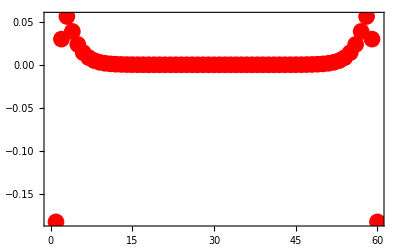

```mathematica
ListPlot[list1,PlotRange->All,Frame->True,PlotStyle-> {Red,PointSize[0.03]},Axes->False]
```

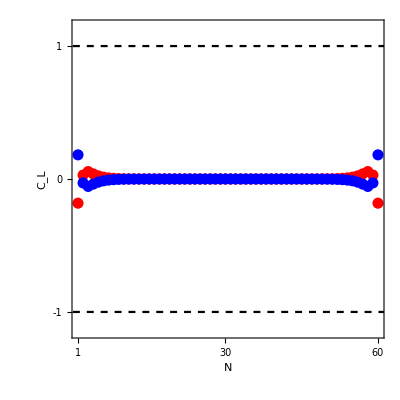

```mathematica
Show[Plot[1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.15,1.15}},Frame->True,Axes->False],
Plot[-1,{x,0,Lx+2},PlotStyle->{Dashed,Black},PlotRange->{{1,Lx},{-1.15,1.15}},Frame->True,Axes->False],
ListPlot[list1,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Red,PointSize[0.02]},Axes->False],
ListPlot[list2,PlotRange->{-1.2,1.2},Frame->True,PlotStyle-> {Blue,PointSize[0.02]},Axes->False],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 24,
FrameTicks->{ {{{-1,"-1"},{0,"0"},{1,"1"}},None},{{1,Lx/2,Lx},None}},
ImageSize-> 400,AspectRatio-> 1,
FrameLabel->{"N","C_L"},RotateLabel->False]
```